```mathematica
Quit[]
```

```mathematica
file=OpenRead["F:\\LinuxShare\\2014_03\\stau4_LUXCDMS_scaled.dat"];
file2=OpenWrite["F:\\LinuxShare\\2014_03\\stau4_LUXCDMS_scaled_relic.dat"];
list=Import["F:\\Dropbox\\Dropbox\\Study\\LIGHTDM\\exp\\LUX","Table"];
list2=Import["F:\\Dropbox\\Dropbox\\Study\\LIGHTDM\\exp\\supercdms.dat","Table"];
list3=Import["F:\\Dropbox\\Dropbox\\Study\\LIGHTDM\\exp\\Delphi_stau.dat","Table"];
```

```mathematica
findval[x_,datalist_]:=Quiet[(i=1;While[x≥ datalist[[i,1]]&&i≤Length[datalist],i++];If[i> Length[datalist]||i==1,1,Exp[Log[datalist[[i-1,2]]]+(Log[datalist[[i,2]]]-Log[datalist[[i-1,2]]])*(Log[x]-Log[datalist[[i-1,1]]])/(Log[datalist[[i,1]]]-Log[datalist[[i-1,1]]])]])]
```

```mathematica
rules[temp_]:=If[temp[[616]]>=0.09154, True, False]
```

```mathematica
rules[temp_]:=If[temp[[837]]≤ 4.7, True, False]
```

```mathematica
rules[temp_]:=If[temp[[836]](0.23116-temp[[814]]^2/2)^2/(0.23116-temp[[814]]^2)^2≤ 4.7, True, False]
```

```mathematica
rules[temp_]:=(dd=If[(temp[[40]]^2-(temp[[54]]+4.08)^2)/temp[[40]]^2<-0.6||(-0.6<(temp[[40]]^2-(temp[[54]]+4.08)^2)/temp[[40]]^2<0&&temp[[617]]<10^-5)||((temp[[40]]^2-(temp[[54]]+4.08)^2)/temp[[40]]^2>0&&temp[[617]]>10^-8),temp[[617]],5 10^-6];If[dd temp[[616]]/0.1139≤findval[temp[[54]],list]&&dd temp[[616]]/0.1139≤findval[temp[[54]],list2]&&temp[[54]]≤40&&Length[temp]==841, True, False])
```

```mathematica
rules[temp_]:=If[(temp[[40]]^2-(temp[[54]]+4.08)^2)/temp[[40]]^2<-0.6||(-0.6<(temp[[40]]^2-(temp[[54]]+4.08)^2)/temp[[40]]^2<0&&temp[[617]]<10^-5)||((temp[[40]]^2-(temp[[54]]+4.08)^2)/temp[[40]]^2>0&&temp[[617]]>10^-8),True,False]
```

```mathematica
rules[temp_]:=If[temp[[616]]≥0.001&&temp[[54]]≤40&&Length[temp]==841&&temp[[51]]>81.9&&(0.23116-temp[[814]]^2/2)^2/128*91187/4/0.23116/(1-0.23116)*(1-4*temp[[50]]^2/91.187^2)^1.5 <4.7&&temp[[54]]≥findval[temp[[50]],list3], True, False]
```

```mathematica
rules[temp_]:=(dd=temp[[617]];If[dd temp[[616]]/0.1139≤findval[temp[[54]],list]&&dd temp[[616]]/0.1139≤findval[temp[[54]],list2]&&temp[[54]]≤40&&Length[temp]==841, True, False])
```

```mathematica
j=0;
While[True,out=Read[file,String];j++;If[Mod[j,5000]==0,Print[j]];If[out==EndOfFile,Break[]];temp=ToExpression[StringReplace[StringSplit[out],"E"->" 10^"]];If[rules[temp],WriteString[file2,out,"\n"]]]
Close[file];
Close[file2];
```

5000

```mathematica
Length[temp]
```

841

```mathematica
listnew=Table[list[[i]],{i,1,Length[list]}];
```

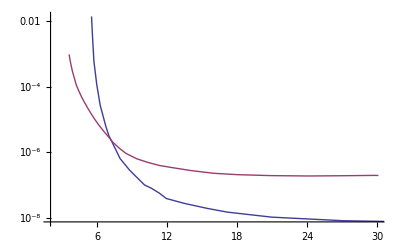

```mathematica
ListLogPlot[{list,list2},Joined->True,PlotRange->{{2,30},Full}]
```

```mathematica
file=OpenRead["/home/zhen/Dropbox/Study/datashare/figure3/dec/dec_dm_higgs_coll_flav.dat"];
file2=OpenWrite["/home/zhen/Dropbox/Study/datashare/figure3/dec/dec_dm_higgs_coll_flav_new.dat"];
While[True,out=Read[file,String];If[out==EndOfFile,Break[]];temp=ToExpression[StringReplace[StringSplit[out],"E"->" 10^"]];temp2=ToString[ScientificForm[temp,{5,4},NumberMultiplier->"",NumberFormat:>(If[#3≠"",Row[{#1,"E",If[ToExpression[#3]≥0,If[ToExpression[#3]≥10,StringJoin["+",#3],StringJoin["+0",#3]],If[ToExpression[#3]≤-10,#3,StringReplace[#3,"-"->"-0"]]]}],Row[{#1,"E","+00"}]]&),NumberPadding->{" ","0"}]];WriteString[file2,StringTrim[StringReplace[temp2,{","->"","{"->"","}"->""," -"->"  -"}]],"\n"]];
Close[file];
Close[file2];
```

```mathematica
file=OpenRead["/home/zhen/Dropbox/Study/datashare/figure3/dec/dec_dm_higgs_coll_flav_xenon2012.dat"];
file2=OpenWrite["/home/zhen/Dropbox/Study/datashare/figure3/dec/dec_dm_higgs_coll_flav_xenon2012_new.dat"];
```

```mathematica
out=Read[file,String]
```

0  60.57  23.85  1.071E-01  2.98E-31 61.66  141.28  935.64  8.29  -3868.30 889.04  2589.00  2580.00  3000.00  1.78E-04  2.04E-11  3.49E-04  3.24E-04  2.97E-09  9.95E-01  9.37E-11  1.66E-07  9.61E-11  1.43E-07  123.81  3.33E-03  889.36  1.88E+00  889.04  1.81E+00  892.95  1.62E+00

```mathematica
temp=ToExpression[StringReplace[StringSplit[out],"E"->" 10^"]]
```

{0,60.57,23.85,0.1071,2.98×10^-31,61.66,141.28,935.64,8.29,-3868.3,889.04,2589.,2580.,3000.,0.000178,2.04×10^-11,0.000349,0.000324,2.97×10^-9,0.995,9.37×10^-11,1.66×10^-7,9.61×10^-11,1.43×10^-7,123.81,0.00333,889.36,1.88,889.04,1.81,892.95,1.62}

```mathematica
%4//FortranForm
```

List(0,292.8,26.63,0.1179,5.8700000000000005e-27,296.2,854.27,680.49,21.5,-2572.3,642.11,2804.5,2508.4,3000.,0.000050700000000000006,8.92e-11,
     -  0.000361,0.000323,3.1000000000000005e-9,0.9400000000000001,1.45e-9,9.82e-7,1.5000000000000002e-9,7.91e-7,127.81,0.00319,642.21,5.1,642.11,5.12,
     -  647.31,4.6)

```mathematica
ScientificForm[%4,5]
```

{0,2.928×10^2,2.663×10^1,1.179×10^-1,5.87×10^-27,2.962×10^2,8.5427×10^2,6.8049×10^2,2.15×10^1,-2.5723×10^3,6.4211×10^2,2.8045×10^3,2.5084×10^3,3.×10^3,5.07×10^-5,8.92×10^-11,3.61×10^-4,3.23×10^-4,3.1×10^-9,9.4×10^-1,1.45×10^-9,9.82×10^-7,1.5×10^-9,7.91×10^-7,1.2781×10^2,3.19×10^-3,6.4221×10^2,5.1,6.4211×10^2,5.12,6.4731×10^2,4.6}

```mathematica
NumberForm[%24,NumberFormat->(Row[{#1,"E",#3}]&)]
```

{0E,292.8E,26.63E,0.1179E,5.87E-27,296.2E,854.27E,680.49E,21.5E,-2572.3E,642.11E,2804.5E,2508.4E,3000.E,0.0000507E,8.92E-11,0.000361E,0.000323E,3.1E-9,0.94E,1.45E-9,9.82E-7,1.5E-9,7.91E-7,127.81E,0.00319E,642.21E,5.1E,642.11E,5.12E,647.31E,4.6E}

```mathematica
InputForm[ToString[NumberForm[N[%4],5,NumberFormat:>(If[#3≠"",Row[{#1,"E",#3}],Row[{#1,"E","0"}]]&)]]]
```

"{0.E0, 292.8E0, 26.63E0, 0.1179E0, 5.87E-27, 296.2E0, 854.27E0, 680.49E0, 21.5E0, -2572.3E0, 642.11E0, 2804.5E0, 2508.4E0, 3000.E0, 0.0000507E0, 8.92E-11, \
0.000361E0, 0.000323E0, 3.1E-9, 0.94E0, 1.45E-9, 9.82E-7, 1.5E-9, 7.91E-7, 127.81E0, 0.00319E0, 642.21E0, 5.1E0, 642.11E0, 5.12E0, 647.31E0, 4.6E0}"

```mathematica
ScientificForm[temp,{5,4},NumberMultiplier->"",NumberFormat:>(If[#3≠"",Row[{#1,"E",#3}],Row[{#1,"E","+00"}]]&),NumberPadding->{"_","0"}]//ToString
```

{_0.0000E+00, _2.9280E2, _2.6630E1, _1.1790E-1, _5.8700E-27, _2.9620E2, _8.5427E2, _6.8049E2, _2.1500E1, -2.5723E3, _6.4211E2, _2.8045E3, _2.5084E3, _3.0000E3, _5.0700E-5, _8.9200E-11, _3.6100E-4, _3.2300E-4, _3.1000E-9, _9.4000E-1, _1.4500E-9, _9.8200E-7, _1.5000E-9, _7.9100E-7, _1.2781E2, _3.1900E-3, _6.4221E2, _5.1000E+00, _6.4211E2, _5.1200E+00, _6.4731E2, _4.6000E+00}

```mathematica
ToString[ScientificForm[temp,{5,4},NumberMultiplier->"",NumberFormat:>(If[#3≠"",Row[{#1,"E",If[ToExpression[#3]≥0,If[ToExpression[#3]≥10,StringJoin["+",#3],StringJoin["+0",#3]],If[ToExpression[#3]≤-10,#3,StringReplace[#3,"-"->"-0"]]]}],Row[{#1,"E","+00"}]]&),NumberPadding->{" ","0"}]]//ToString
```

{ 0.0000E+00,  6.0570E+01,  2.3850E+01,  1.0710E-01,  2.9800E-31,  6.1660E+01,  1.4128E+02,  9.3564E+02,  8.2900E+00, -3.8683E+03,  8.8904E+02,  2.5890E+03,  2.5800E+03,  3.0000E+03,  1.7800E-04,  2.0400E-11,  3.4900E-04,  3.2400E-04,  2.9700E-09,  9.9500E-01,  9.3700E-11,  1.6600E-07,  9.6100E-11,  1.4300E-07,  1.2381E+02,  3.3300E-03,  8.8936E+02,  1.8800E+00,  8.8904E+02,  1.8100E+00,  8.9295E+02,  1.6200E+00}

```mathematica
%105//ToString
```

{0E0, 2.928E2, 2.663E1, 1.179E-1, 5.87E-27, 2.962E2, 8.5427E2, 6.8049E2, 2.15E1, -2.5723E3, 6.4211E2, 2.8045E3, 2.5084E3, 3.E3, 5.07E-5, 8.92E-11, 3.61E-4, 3.23E-4, 3.1E-9, 9.4E-1, 1.45E-9, 9.82E-7, 1.5E-9, 7.91E-7, 1.2781E2, 3.19E-3, 6.4221E2, 5.1E0, 6.4211E2, 5.12E0, 6.4731E2, 4.6E0}

```mathematica
StringTrim[StringReplace[%,{","->"","{"->"","}"->""," -"->"  -"}]]
```

0.0000E+00  6.0570E+01  2.3850E+01  1.0710E-01  2.9800E-31  6.1660E+01  1.4128E+02  9.3564E+02  8.2900E+00  -3.8683E+03  8.8904E+02  2.5890E+03  2.5800E+03  3.0000E+03  1.7800E-04  2.0400E-11  3.4900E-04  3.2400E-04  2.9700E-09  9.9500E-01  9.3700E-11  1.6600E-07  9.6100E-11  1.4300E-07  1.2381E+02  3.3300E-03  8.8936E+02  1.8800E+00  8.8904E+02  1.8100E+00  8.9295E+02  1.6200E+00

```mathematica
Export["~/Desktop/data.dat", %, "String"]
```

~/Desktop/data.dat

```mathematica
WriteString[file2,%13,"\n"]
```

```mathematica
Close[file2]
```

/home/zhen/Dropbox/Study/datashare/figure3/dec/dec_dm_higgs_coll_flav_xenon2012_new.dat

```mathematica
Round[%70,0.00001]
```

{{0.,0.},{0.2928,3.},{0.2663,2.},{0.1179,0.},{0.587,-26.},{0.2962,3.},{0.85427,3.},{0.68049,3.},{0.215,2.},{-0.25723,4.},{0.64211,3.},{0.28045,4.},{0.25084,4.},{0.3,4.},{0.507,-4.},{0.892,-10.},{0.361,-3.},{0.323,-3.},{0.31,-8.},{0.94,0.},{0.145,-8.},{0.982,-6.},{0.15,-8.},{0.791,-6.},{0.12781,3.},{0.319,-2.},{0.64221,3.},{0.51,1.},{0.64211,3.},{0.512,1.},{0.64731,3.},{0.46,1.}}

0.2928

```mathematica
ScientificForm[2.98*10^2,{12,4},NumberMultiplier->"",NumberFormat:>(If[#3≠"",Row[{#1,"E",If[ToExpression[#3]≥0,If[ToExpression[#3]≥10,StringJoin["+",#3],StringJoin["+0",#3]],If[ToExpression[#3]≤-10,#3,StringReplace[#3,"-"->"-0"]]]}],Row[{#1,"E","+00"}]]&),NumberPadding->{" ","0"}]
```

2.9800E+02

```mathematica
NumberForm[2,NumberFormat->]
```

022

```mathematica
StringPart
```

```mathematica
ToString[ToString[#,FortranForm]&/@%24]
```

{0, 292.8, 26.63, 0.1179, 5.8700000000000005e-27, 296.2, 854.27, 680.49, 21.5, -2572.3, 642.11, 2804.5, 2508.4, 3000., 0.000050700000000000006, 8.92e-11, 0.000361, 0.000323, 3.1000000000000005e-9, 0.9400000000000001, 1.45e-9, 9.82e-7, 1.5000000000000002e-9, 7.91e-7, 127.81, 0.00319, 642.21, 5.1, 642.11, 5.12, 647.31, 4.6}

```mathematica
StringJoin[ToString/@PadLeft[Characters[ToString[%95[[2]]]],9]]
```

0000292.8